# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

[MinD] = 2.5 µM
[MinE-His] = 5 µM

```mathematica
img=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch2_2.5uM-MinD_5uM-E-His_snap01.lsm"];
```

```mathematica
img2=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch2_2.5uM-MinD_5uM-E-His_snap02.lsm"];
```

Separate MinD and MinE channels

```mathematica
imgSep=ColorSeparate[img];
imgSep2=ColorSeparate[img2];
```

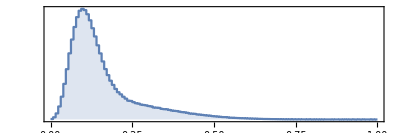
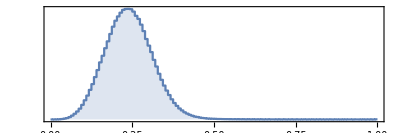

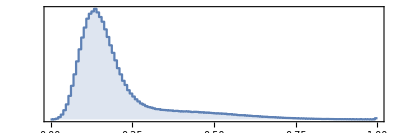
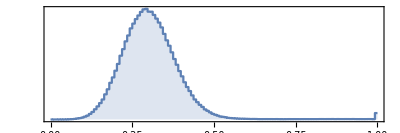

```mathematica
ImageHistogram/@ImageAdjust/@imgSep
ImageHistogram/@ImageAdjust/@imgSep2
```

```mathematica
imgReg={ImageAdjust[ImageAdjust@imgSep[[1]],0,{0,0.55}],ImageAdjust@imgSep[[2]]};
imgReg2={ImageAdjust[ImageAdjust@imgSep2[[1]],0,{0,0.7}],ImageAdjust@imgSep2[[2]]};
```

```mathematica
colorMap={minD,minE,minE+minD/1.5};
```

Image 1, Extended Data Fig. 1c

```mathematica
imgColor=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg))
```

Image 2, Extended Data Fig. 1c

```mathematica
imgColor2=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg2))
```

## Image preparation

### MinD-MinE pixel clustering (using first image)

```mathematica
classImage=BrightnessEqualize[ImageAdjust[#]]&/@imgSep;
```

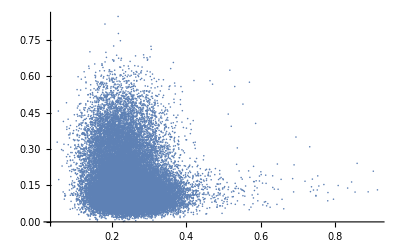

```mathematica
ListPlot[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}[[All,;;200,;;200]]],PlotRange->All]
```

```mathematica
clusters=FindClusters[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}],2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

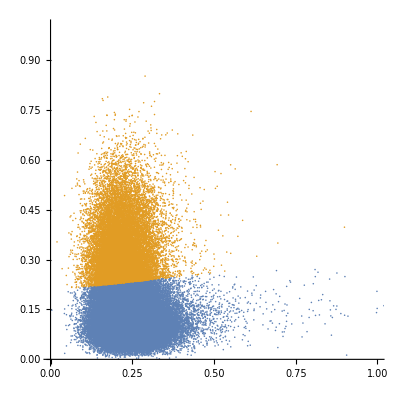

```mathematica
ListPlot[clusters[[All,;;;;10]],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
centroids=Mean/@clusters;
```

```mathematica
ratioDE=#[[1]]/#[[2]]&@First@Differences[centroids]
```

-0.107713

### Mesh binarization

```mathematica
ClearAll@meshBinarize;
Options[meshBinarize]={"ThresholdPixelNumber"->10};
meshBinarize[img_,ratioDE_,opts:OptionsPattern[]]:=Block[
{imgEq=BrightnessEqualize[ImageAdjust[#]]&/@img,
minDMeas,
minE,
minD,
imgProj,
imgBinarized,
morphImg,
smallComponents,
morphMask,
imgBinarizedCleaned
},
minDMeas=ImageMeasurements[imgEq[[2]],{"Mean","StandardDeviation"}];
minE=imgEq[[1]];
(*to ignore MinD aggregates, cut brightness at mean+std off*)
minD=ImageClip[imgEq[[2]],{0,Total@minDMeas}];
(*project pixel MinD MinE fluorescence values on the axis connecting the centroids of the clusters identified in the initial image*)
imgProj=Image[ImageData[minE]+ratioDE ImageData[minD]];
(*binarize along this axis, and smooth to get a connected mesh*)
imgBinarized=Binarize[GaussianFilter[Binarize[ImageAdjust@imgProj],5],0.3];

(*remove too small morphological components*)
morphImg=MorphologicalComponents[imgBinarized];
smallComponents=Keys@Select[ComponentMeasurements[morphImg,"Area"],#[[2]]<10&];
morphMask=Clip[morphImg/.Thread[smallComponents->-1],{-1,0}];
imgBinarizedCleaned=Image[ImageData[imgBinarized]+morphMask];

{imgProj,imgBinarizedCleaned}
]
```

```mathematica
imgProj=meshBinarize[imgSep,ratioDE];
```

```mathematica
imgProj2=meshBinarize[imgSep2,ratioDE];
```

Skeleton of the network

```mathematica
branchIm=Thinning[imgProj[[2]]]
```

-Graphics-

```mathematica
branchIm2=Thinning[imgProj2[[2]]];
```

## Analysis

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

## Determine branch points

The branch width is about 3 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined (repeatedly to account for short, branched segments that we want to remove).

```mathematica
branchImPrun=Thinning[Pruning[Pruning[Pruning[branchIm,10],10],10]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints[Binarize@branchImPrun];
```

```mathematica
branchPointCoords=ImageValuePositions[branchPoints,1];
```

```mathematica
HighlightImage[branchImPrun,{AbsolutePointSize[3],branchPointCoords}]
```

-Graphics-

```mathematica
branchImPrun2=Thinning[Pruning[Pruning[Pruning[branchIm2,10],10],10]];
branchPoints2=MorphologicalBranchPoints[Binarize@branchImPrun2];
branchPointCoords2=ImageValuePositions[branchPoints2,1];
```

## Average branch widths (using first image)

Determine average branch width by binarizing the experimental network image (imgProj[[1]]) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

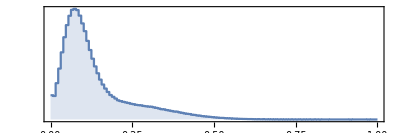

```mathematica
ImageHistogram[imgProj[[1]]]
```

Set 0.4 as branch intensity maximum and 0.1 as intensity minimum (intensity of plateaus)

```mathematica
width=N@Total@Flatten@ImageData[Binarize[ImageAdjust[imgProj[[1]],0,{0.1,0.4}],0.5]]/(Total@Flatten@ImageData@branchIm)
```

2.77677

## Vertices - Image 1

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords,0.]]}]/@branchPointCoords,#[[-1]]>10&];
Length@tripleVerticesRaw
```

1170

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices=Block[{
tvs=tripleVerticesRaw,
branches=branchImPrun,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices
```

1164

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Complement[branchPointCoords,tripleVertices[[All,1]]];
quadrupleVertices=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw],I];
Length@quadrupleVertices
```

276

```mathematica
vertices=Join[tripleVertices,quadrupleVertices];
```

```mathematica
HighlightImage[branchIm,{AbsolutePointSize[3],tripleVertices,AbsolutePointSize[6],quadrupleVertices}]
```

-Graphics-

## Analysis of triple vertices - Image 1

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

1164

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
Show[
HighlightImage[imgProj[[1]],{AbsolutePointSize[5],tripleVertices}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{255,150,20}/255]},
Circle[#,3]&/@quadrupleVertices]]
]
```

-Graphics-

```mathematica
angles3=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

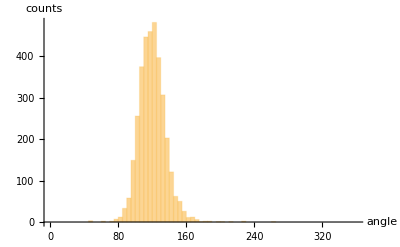

```mathematica
Histogram[{
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,1]]
```

15.606

#### FitList

```mathematica
vertex3MeasurementsRaw
```

### Fit result

```mathematica
Show[
imgColor,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices]]
]
```

## Vertices - Image 2

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw2=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords2,0.]]}]/@branchPointCoords2,#[[-1]]>10&];
Length@tripleVerticesRaw2
```

661

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices2=Block[{
tvs=tripleVerticesRaw2,
branches=branchImPrun2,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices2
```

661

### 4-fold vertices

```mathematica
quadrupleVerticesRaw2=Complement[branchPointCoords2,tripleVertices2[[All,1]]];
quadrupleVertices2=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw2[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw2],I];
Length@quadrupleVertices2
```

90

```mathematica
vertices2=Join[tripleVertices2,quadrupleVertices2];
```

```mathematica
HighlightImage[branchIm2,{AbsolutePointSize[3],tripleVertices2,AbsolutePointSize[6],quadrupleVertices2}]
```

-Graphics-

## Analysis of triple vertices - Image 2

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj2[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices2}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw2=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw2,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

661

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
angles32=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

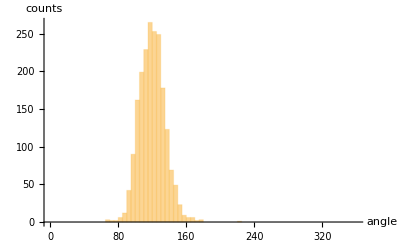

```mathematica
Histogram[{
Flatten[angles32,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles32,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles32,1]]
```

15.0546

#### FitList

```mathematica
vertex3MeasurementsRaw2
```

{{157.231,1000.7,-1.60628,0.00688191,3.11756},{247.371,991.615,-1.63629,0.4657,2.74088},{278.434,988.414,-1.6174,0.298976,2.4849},{110.472,983.176,-2.38851,-0.168649,2.23196},{880.116,983.346,-1.64695,0.60677,2.7853},{381.611,982.734,-1.70716,1.37937,3.0942},{804.526,981.952,-2.13366,-0.109877,2.19639},{123.177,981.027,-1.03068,0.777464,2.9567},{831.316,979.299,-0.886911,0.836534,3.04719},{647.167,977.269,-2.75497,-0.781351,1.75165},{758.253,971.68,-2.59618,-0.251089,1.48635},{926.166,971.74,-1.4549,0.77028,2.66074},{329.566,969.306,-1.67558,0.738502,2.70742},{429.306,969.683,-2.97344,-0.817558,1.44366},{796.663,968.663,-1.33887,1.05191,2.9117},{411.518,966.526,-2.33247,0.187737,2.36042},{661.307,964.356,-1.74896,0.235292,2.41422},{81.3061,962.383,-1.98215,0.447774,2.24332},{243.721,956.735,-2.69794,-0.376444,1.43642},{462.558,953.775,-3.04259,-0.562363,1.1682},{595.123,953.948,-1.31736,1.13553,3.12257},{716.675,953.802,-1.98343,-0.0241743,2.29743},{733.473,953.268,-0.957653,0.754355,3.10024},{396.964,951.806,-1.56982,0.784266,2.64698},{446.497,951.518,-1.96882,0.169734,2.32605},{213.196,948.231,-2.2405,0.0999749,1.83956},{271.937,948.495,-1.22968,1.24306,2.99657},{474.943,945.84,-1.23434,0.360214,2.54545},{73.1166,943.86,-3.02896,-0.88085,1.16327},{119.809,942.248,-2.24651,0.565308,2.40558},{563.213,941.225,-2.8893,-0.825001,0.77645},{40.5004,939.497,-2.20648,0.151244,2.02022},{547.209,937.287,-2.38366,0.208765,2.07757},{276.093,936.357,-2.29208,-0.260116,1.88117},{802.501,934.499,-2.4359,-0.473287,1.71088},{182.798,931.786,-2.6815,-0.134007,1.72163},{933.791,931.383,-2.48002,-0.220011,1.71739},{325.002,930.596,-2.30764,-0.0795,1.56009},{886.409,931.266,-1.73573,-0.018298,2.30334},{986.529,930.509,-2.5804,-0.485541,1.80087},{199.285,929.752,-1.03632,0.961296,3.02047},{88.8909,926.046,-1.96527,0.0528774,2.34767},{106.121,926.994,-3.07807,-1.21787,0.671261},{927.274,926.469,-1.59259,0.589066,2.80264},{485.217,922.847,-1.4025,0.332179,2.05195},{396.334,921.081,-2.88711,-0.465512,1.5106},{315.773,920.31,-1.72936,0.818311,2.69279},{834.6,920.75,-1.38689,0.839266,2.8149},{964.309,918.984,-1.68722,0.39153,2.71534},{382.626,917.523,-1.97382,0.253961,2.38941},{757.581,916.178,-2.33797,-0.624701,2.19902},{314.021,909.409,-2.58875,-0.858629,1.39802},{655.47,907.59,-2.77329,-0.578069,1.72065},{770.485,908.485,-1.2744,0.600132,2.75547},{696.504,907.497,-2.80444,-0.580858,1.23792},{80.1871,903.148,-2.96866,-0.880809,1.23734},{218.265,901.924,-2.00703,-0.261478,2.23734},{489.469,901.246,-2.47312,-0.325208,1.78563},{629.267,901.049,-2.17332,0.0893519,2.1561},{249.532,899.881,-2.54285,-0.516495,1.24263},{521.518,899.517,-2.79247,-0.703902,1.00895},{919.686,899.714,-2.93559,-1.11173,1.10443},{579.509,898.499,-2.31461,-0.128072,1.6913},{43.3578,898.357,-1.55578,0.169589,2.5288},{670.143,898.088,-1.34019,0.345873,2.55972},{880.538,896.011,-2.81649,-0.491424,1.50471},{240.533,893.993,-1.50051,0.559654,2.59615},{508.728,894.647,-1.58438,0.42231,2.80093},{623.937,892.736,-1.51467,1.02558,2.96131},{890.857,890.625,-1.57111,0.456289,2.6326},{725.423,887.909,-1.49947,0.60769,2.45576},{93.4152,886.674,-1.70136,0.399598,2.24029},{280.503,884.496,-1.41838,0.633098,2.72307},{467.594,884.855,-1.94418,0.616281,2.53779},{330.506,882.506,-2.47238,-0.558896,2.01816},{960.485,879.494,-2.55844,-0.481652,1.58146},{204.818,877.492,-2.85809,-1.1902,0.987624},{622.504,877.4,-2.61812,-0.999899,1.40874},{726.298,875.422,-2.3076,-0.402927,1.64104},{357.18,872.226,-3.05949,-0.988429,1.01306},{423.5,872.503,-2.68947,-0.340479,1.49145},{558.493,871.129,-1.25707,0.974876,2.63493},{680.113,864.837,-2.50983,-0.309651,1.93423},{459.028,864.536,-0.965331,1.09758,3.00831},{987.86,863.977,-1.91397,0.4972,2.58787},{402.97,863.701,-3.00545,-1.27285,0.357093},{899.848,859.496,-2.04265,0.127714,2.09861},{563.281,855.811,-2.339,-0.245206,1.86456},{65.5103,855.48,-2.18214,0.177375,2.25515},{368.678,854.993,-2.17481,0.306378,2.1721},{707.695,854.917,-1.5096,0.824083,2.75029},{466.097,854.57,-1.94398,-0.0810378,2.17767},{847.734,849.608,-2.18318,-0.0699966,1.77243},{585.884,849.006,-1.03607,0.758133,2.80971},{493.123,847.297,-1.18396,0.870565,2.74444},{893.876,847.324,-3.1058,-0.961668,1.13016},{938.115,848.208,-2.43573,-0.594312,1.57786},{260.71,846.205,-2.13249,0.145254,2.13643},{795.587,844.431,-3.01431,-0.645493,1.58249},{210.841,842.186,-2.93732,-0.595414,1.60728},{630.797,841.752,-2.75611,-0.479261,1.50141},{360.36,843.494,-2.72104,-1.16226,0.946053},{192.554,838.45,-2.3993,0.182497,2.131},{145.167,836.408,-2.35155,-0.480015,1.73022},{839.068,837.518,-2.96669,-1.02416,0.939435},{594.341,834.678,-1.77587,0.0632804,2.12836},{499.99,830.762,-2.2505,-0.2069,1.97863},{813.494,830.518,-1.68527,0.354487,2.48153},{707.194,828.405,-2.97113,-0.672458,1.44852},{732.209,827.241,-2.66465,-0.0141111,1.44841},{760.231,830.296,-2.9173,-1.24117,1.02808},{908.979,828.501,-1.58703,0.470583,2.28251},{37.6966,827.72,-2.86939,-0.783742,0.967051},{23.4997,823.508,-1.89145,0.286855,2.44891},{174.689,821.277,-1.45196,0.783364,2.67718},{718.053,819.718,-1.60462,0.508574,2.46328},{530.084,818.923,-1.47777,0.589811,2.59305},{94.0621,815.689,-2.64087,-0.435193,1.6495},{240.46,815.476,-1.72786,0.43743,2.43857},{462.717,811.652,-2.15225,0.11418,1.96234},{238.566,806.438,-2.56921,-0.529476,1.33875},{119.781,804.4,-1.29372,0.900408,2.78928},{418.251,803.119,-2.40901,0.132827,1.87472},{859.497,804.5,-2.45665,-0.32897,2.11959},{61.7894,802.45,-1.69948,0.296427,2.29537},{304.505,800.488,-2.34226,0.418579,2.28066},{338.502,797.894,-1.19843,0.651296,2.47432},{532.205,799.354,-2.34071,-0.616106,1.70357},{717.491,798.506,-2.45711,-0.613398,1.55001},{909.112,796.033,-2.75362,-0.372128,1.58009},{122.315,796.205,-2.15104,-0.325206,1.85553},{17.3035,793.372,-2.28667,-0.402715,1.46142},{652.381,792.885,-2.30087,-0.070737,1.78804},{812.526,792.667,-2.5848,-0.284028,1.6498},{178.931,791.688,-2.61159,-0.286134,1.73264},{387.331,790.087,-2.27716,-0.140532,1.95964},{597.445,789.213,-2.22949,-0.0385291,2.20726},{401.28,788.606,-1.09386,0.666542,3.05926},{890.501,788.517,-1.98993,0.386274,2.46783},{933.08,788.496,-0.96574,0.983762,2.89486},{768.821,784.244,-2.62094,-0.694885,1.72907},{836.554,785.723,-1.4012,0.687728,2.85961},{203.846,784.159,-1.66293,0.654987,2.8376},{643.497,783.51,-1.34084,0.793453,2.73973},{58.2959,781.327,-1.5426,1.37819,2.95572},{263.196,783.536,-2.05126,-0.0668833,2.33449},{282.375,781.385,-1.12225,0.625122,2.98983},{151.907,775.74,-1.72415,0.531571,2.46893},{741.052,776.3,-2.11059,0.0594831,2.24923},{347.886,772.516,-2.48056,-0.285598,1.8997},{784.64,772.877,-1.3989,0.743065,2.69114},{943.908,772.262,-1.67477,-0.0466575,2.13637},{570.467,768.578,-1.82684,0.360398,2.1803},{60.4938,767.501,-2.00459,-0.25657,1.81493},{497.497,767.506,-1.61642,0.565166,2.48574},{972.499,767.509,-1.69156,0.481567,2.82637},{364.553,766.762,-1.10346,0.77219,2.78854},{339.678,766.656,-3.13522,-1.53957,0.584277},{106.495,764.497,-2.54472,-0.612358,1.30416},{732.891,760.918,-1.58408,1.11218,2.90405},{785.602,761.142,-2.25386,-0.581329,1.57195},{644.86,760.126,-2.58263,-1.01315,1.47401},{96.1995,757.299,-1.48266,0.640239,2.86677},{298.647,755.822,-1.70296,0.336949,2.25378},{449.506,755.499,-2.5535,-0.72367,1.48494},{881.349,750.937,-2.46739,-0.50129,1.32093},{143.396,747.069,-1.33291,1.10119,2.96504},{433.501,745.505,-1.59918,0.518361,2.41663},{654.773,744.382,-2.13938,-0.0319044,2.17216},{564.646,742.77,-2.65179,-0.475778,1.37125},{676.856,743.778,-0.95152,0.952716,3.13064},{944.473,742.09,-2.41639,-0.14932,1.75785},{732.504,741.493,-2.52228,-0.71352,1.52922},{965.8,738.828,-0.714613,1.24162,2.98744},{44.9868,738.214,-3.08645,-0.937103,0.951965},{22.1247,736.993,-1.94399,0.0578549,2.24197},{494.596,735.755,-2.89932,-0.705141,1.43263},{146.972,733.502,-2.37659,-0.0162783,1.8765},{474.958,731.026,-2.16024,0.225136,2.3797},{586.774,732.226,-1.15922,0.560603,2.73264},{743.124,732.565,-1.84861,-0.0124856,2.47754},{759.128,731.988,-1.00451,0.817081,3.11001},{933.752,732.19,-1.66136,0.750958,2.87352},{547.847,731.323,-2.97567,-1.19842,0.676785},{336.391,728.498,-2.47267,-0.445487,1.3944},{689.874,726.191,-1.61475,0.436726,2.22702},{825.388,724.78,-1.88942,0.323941,2.12943},{506.399,725.472,-1.71851,0.160777,2.41644},{433.88,722.999,-2.38964,-0.228184,1.66271},{239.049,722.332,-1.01948,1.34668,2.97648},{378.852,722.255,-3.05652,-0.804698,1.57253},{301.452,720.106,-2.44545,-0.126143,1.88722},{321.282,717.008,-1.19098,0.639401,2.93146},{465.971,716.671,-1.52032,1.03204,2.93934},{427.069,716.794,-1.35502,0.72105,3.00444},{387.5,713.503,-1.80333,0.313774,2.37903},{931.501,711.498,-2.56796,-0.666759,1.44567},{819.595,705.787,-3.09373,-1.23436,1.3028},{601.498,704.498,-2.37187,-0.362503,2.13562},{269.803,701.834,-1.35691,0.661162,2.79192},{781.61,701.125,-2.01348,0.211836,2.21828},{874.665,701.176,-1.72936,0.217047,2.14616},{687.844,699.342,-2.52981,-0.455525,1.47592},{916.336,700.986,-1.73222,0.660849,2.9367},{632.8,691.255,-3.04821,-0.807865,1.12549},{557.734,689.658,-2.19367,-0.15681,1.68834},{622.323,689.937,-2.43431,0.153989,2.13236},{123.519,686.52,-2.44658,-0.661071,1.79783},{377.486,685.926,-3.02744,-1.0477,1.1638},{582.106,685.89,-1.06024,0.754345,2.99117},{732.947,683.088,-2.94319,-0.494593,1.32493},{29.6529,683.915,-1.71929,0.501971,2.51238},{465.495,683.502,-2.64089,-0.628682,1.4967},{340.251,682.041,-2.01595,0.0527717,2.11448},{722.061,681.242,-2.06404,0.146786,2.48308},{872.108,682.105,-2.64031,-0.847525,1.47734},{965.929,678.057,-1.78143,0.466329,2.3204},{505.495,677.507,-2.6549,-0.82623,1.56565},{651.078,675.484,-1.29404,0.562903,2.49839},{438.183,672.196,-2.07476,0.283574,1.95729},{753.861,671.328,-1.05194,1.052,2.64158},{182.502,671.493,-2.93756,-0.585162,1.25014},{269.955,670.841,-2.01514,-0.37077,1.38587},{334.328,669.33,-2.97711,-1.03779,1.15023},{593.362,667.35,-1.58897,0.453395,2.14388},{883.172,669.96,-1.8698,0.0599991,2.31467},{486.941,667.694,-1.6364,0.481335,2.50054},{389.113,663.51,-2.2088,-0.200598,2.00288},{839.963,663.236,-1.91296,0.555949,2.21497},{78.5749,662.314,-2.40272,-0.169084,1.84144},{150.802,662.548,-1.72335,0.46569,2.72341},{94.5631,659.649,-1.2966,0.887184,2.98173},{299.532,659.54,-1.10588,0.406682,2.79887},{656.499,656.509,-2.22383,-0.350884,1.84002},{761.396,657.442,-1.85154,-0.140486,2.05766},{25.5054,655.493,-2.59328,-0.557218,1.42904},{954.669,652.306,-1.29324,0.907665,2.79389},{378.385,649.341,-3.12417,-1.09795,0.9237},{258.824,648.922,-2.47252,-0.876859,1.05449},{148.44,645.432,-2.91841,-1.03142,1.4336},{683.985,646.131,-1.05121,0.608984,2.77345},{878.628,644.468,-2.63999,-0.261143,1.49265},{203.685,645.686,-2.09636,-0.302682,1.96328},{591.266,642.686,-2.56878,-0.651898,1.42217},{51.9679,641.457,-1.1555,0.608824,2.70895},{482.894,640.145,-1.08835,1.30811,3.01876},{902.391,640.47,-1.97143,-0.822169,3.05803},{385.082,636.185,-1.97847,-0.106888,2.04485},{640.511,632.495,-2.92675,-0.759676,1.04128},{109.763,631.743,-1.77192,0.385216,2.28565},{959.835,631.102,-2.63732,-0.181817,1.76863},{234.976,629.254,-1.53371,0.628727,2.55261},{751.073,630.431,-2.85901,-1.03636,1.12131},{318.041,628.908,-2.12391,0.0276551,2.20946},{977.513,627.843,-1.26367,0.472219,2.97571},{851.536,624.66,-0.813071,0.815978,2.9248},{107.801,621.165,-2.57304,-0.503806,1.39693},{437.722,617.566,-2.0718,-0.0842163,1.84},{235.865,616.466,-2.39,-0.500838,1.67582},{378.992,617.095,-2.7078,-0.645941,1.30968},{925.497,616.487,-2.0409,-0.011067,2.25067},{938.332,616.524,-3.10914,-1.15738,0.728363},{707.5,613.506,-1.88469,0.102237,2.3097},{765.404,607.959,-1.40498,0.611938,2.17901},{173.168,608.039,-1.59974,0.508162,2.38623},{359.478,608.5,-1.68521,0.36993,2.39078},{279.225,606.037,-2.80048,-0.370277,1.77529},{60.9596,603.592,-3.09221,-0.772066,1.572},{589.55,605.004,-1.6478,0.489543,2.48491},{704.315,602.332,-2.9602,-0.91951,1.34412},{917.13,600.46,-2.8656,-0.978743,1.08837},{299.143,599.117,-1.22049,0.985023,2.82964},{15.1092,599.402,-1.52877,0.289427,2.60643},{258.489,598.505,-1.87084,0.363053,2.36871},{172.767,597.194,-2.5244,-0.387478,1.52654},{498.239,597.511,-2.00511,-0.13693,2.07695},{357.939,596.971,-2.75994,-0.894151,1.41588},{672.079,594.657,-1.85845,0.197893,1.95676},{899.481,595.287,-1.82235,0.288038,2.71965},{542.328,592.188,-1.12389,0.896741,2.95943},{769.724,592.211,-2.11687,-0.0607941,2.11137},{815.028,590.112,-1.16312,0.826027,3.07098},{418.032,588.26,-1.29102,0.881935,2.7582},{206.497,583.512,-1.16448,0.775604,2.69478},{764.586,583.831,-3.06329,-1.20683,1.02157},{547.231,581.156,-1.91892,-0.113019,1.98042},{305.792,579.46,-2.32727,-0.446234,1.87338},{987.943,579.95,-2.66727,-0.952533,1.20173},{665.495,575.505,-2.9943,-0.851997,1.20052},{422.172,574.619,-2.31541,-0.422778,1.90077},{729.925,574.155,-1.86755,0.156307,2.31154},{323.496,570.489,-1.04152,0.610081,2.67},{212.8,570.04,-2.37989,-0.744391,2.03117},{251.789,567.68,-2.37973,-0.244199,1.45078},{18.2887,567.083,-2.26998,-0.185155,1.72153},{415.693,567.511,-1.42484,0.84614,3.1245},{827.153,567.845,-2.10516,-0.288506,2.18204},{377.571,565.641,-1.97605,0.126464,2.05791},{540.833,563.462,-2.9011,-0.931617,1.21728},{886.128,564.454,-2.71799,-0.91842,0.983691},{41.3166,562.607,-1.09308,0.758869,2.94636},{477.691,561.945,-2.91074,-0.799804,0.980926},{286.684,559.82,-1.62688,0.778644,2.93676},{467.231,559.276,-1.66521,0.251929,2.88152},{109.485,556.404,-1.86588,0.282507,2.52317},{868.256,556.891,-1.35172,0.407618,3.09939},{235.465,552.581,-1.46713,0.732184,2.56287},{577.94,550.692,-2.86609,-0.563082,1.39347},{555.507,544.495,-1.87555,0.261297,2.24804},{770.957,544.589,-2.605,-0.729894,1.56053},{901.498,543.496,-2.40789,-0.138805,2.2004},{691.503,542.498,-2.30202,-0.121953,2.13122},{925.223,540.551,-1.11344,1.06826,3.03121},{58.1507,538.798,-1.40475,0.688517,2.31504},{369.845,539.291,-2.50599,-0.420042,1.4211},{716.727,539.148,-0.993253,1.03421,3.00999},{168.925,535.71,-1.7833,0.576909,2.22967},{338.808,534.549,-2.19548,-0.236786,1.82577},{283.411,532.651,-2.89376,-0.848531,1.37237},{881.98,531.293,-1.94035,0.405079,2.31296},{991.653,531.693,-1.73211,0.473351,2.64309},{809.495,530.486,-2.48505,-0.490253,1.31009},{357.621,530.345,-1.34106,0.621335,2.94387},{407.189,527.349,-1.11712,1.21863,2.8997},{623.849,525.288,-2.93199,-1.04457,1.36996},{787.708,523.884,-2.45531,-0.0737685,2.00065},{290.247,525.013,-1.90004,-0.226633,2.31348},{101.249,521.807,-2.68897,-0.254863,1.47627},{612.609,522.398,-2.20811,0.309477,2.22025},{799.656,522.942,-1.26769,0.660036,3.04835},{240.305,520.299,-2.7064,-0.450652,1.69036},{60.8851,518.537,-2.8097,-0.274782,1.66962},{734.158,517.829,-1.72643,0.646995,2.39113},{668.122,517.876,-1.00992,0.801584,3.06179},{248.488,515.527,-1.27945,0.690923,2.60377},{632.484,515.493,-1.42042,0.402875,2.38313},{875.893,515.421,-2.78656,-0.966629,1.23773},{989.044,514.823,-2.72775,-1.04312,1.42461},{163.145,513.01,-2.88262,-0.809527,1.28332},{320.481,513.036,-1.6232,0.782224,2.65829},{83.5083,511.507,-1.44831,0.600334,2.8181},{29.1247,510.472,-1.91341,0.163415,2.55414},{362.934,509.582,-2.35411,-0.629911,1.83211},{144.746,508.53,-2.12796,0.225791,2.73384},{842.342,502.719,-2.14204,0.284246,2.03835},{955.321,501.115,-1.80236,0.348244,2.01847},{591.837,502.566,-1.88005,0.733231,3.0943},{417.102,498.375,-2.85719,-0.808601,1.74829},{454.348,497.955,-2.22473,-0.326546,1.47574},{888.826,498.379,-1.29387,0.465915,2.26924},{563.332,499.779,-1.18792,0.258067,3.05841},{257.256,497.262,-2.12395,-0.500932,2.0956},{750.292,496.988,-1.18937,0.654447,2.90348},{683.899,494.195,-1.83932,0.269931,2.20113},{318.514,493.511,-2.69926,-0.706492,1.45192},{479.287,491.913,-0.576079,1.17732,3.01846},{385.327,490.789,-2.00963,0.179399,2.37629},{528.265,487.925,-2.8571,-1.19665,0.758293},{681.107,484.394,-2.77186,-0.868261,1.29385},{83.3703,483.498,-2.26818,-0.503999,1.43914},{331.722,482.228,-1.22403,0.643875,2.44798},{893.084,482.392,-2.254,-0.234372,1.80248},{438.202,479.006,-1.93907,0.836415,2.45003},{582.172,478.127,-1.20445,1.11092,2.65214},{283.895,478.029,-1.58581,0.379209,2.41239},{500.105,477.72,-1.6461,0.410043,2.51784},{769.,473.397,-1.71444,0.202161,2.45107},{719.126,470.579,-1.40087,0.972825,3.13551},{692.905,469.637,-1.79717,0.0783255,2.23487},{932.499,466.518,-1.81162,0.176812,2.51959},{822.486,464.493,-2.12736,-0.37787,1.91639},{69.8804,463.452,-2.89697,-1.07681,1.11856},{429.672,456.558,-2.4707,-0.796006,1.22027},{151.449,452.422,-1.30121,1.10408,2.84174},{280.505,442.498,-2.62189,-0.373494,1.39851},{868.263,439.142,-1.12621,1.0872,2.54144},{689.516,438.825,-2.73014,-0.297157,1.58632},{492.071,437.826,-3.05303,-0.763266,1.23357},{81.7543,435.871,-2.34902,-0.107131,1.88041},{104.749,433.915,-0.808648,1.15298,3.08554},{649.836,434.433,-2.85912,-0.729534,1.57085},{539.747,432.119,-3.05864,-0.442264,1.60272},{455.211,432.766,-1.54972,0.18377,2.39212},{721.519,432.314,-1.01441,1.32442,3.07823},{37.4876,430.507,-1.67572,-0.144293,1.87928},{498.411,431.743,-1.91592,-0.0428937,2.35967},{762.695,429.899,-2.78825,-0.65854,1.38175},{816.418,429.922,-2.61778,-0.279554,1.65884},{156.903,429.283,-2.64267,-0.520882,1.77382},{261.074,428.08,-1.46646,0.756012,2.78073},{920.018,428.882,-2.99043,-0.907791,1.24599},{958.041,427.462,-2.78626,-0.670293,1.743},{657.827,427.004,-1.59227,0.380324,2.38024},{874.984,424.537,-1.59836,0.169001,2.01848},{557.504,423.504,-1.3743,0.748318,2.67605},{69.3763,422.702,-1.43517,0.841831,2.83071},{201.154,423.112,-1.64218,1.02861,3.01765},{612.868,423.035,-2.00935,0.21837,2.30469},{727.663,422.025,-1.96217,0.0174216,2.10735},{173.065,420.068,-1.11571,0.386654,2.64285},{927.872,418.431,-1.91357,0.158401,2.20704},{977.531,418.488,-1.20507,1.05329,2.98159},{393.359,414.913,-1.12549,1.08139,2.64134},{795.903,414.799,-2.96067,-0.306399,0.862184},{127.514,412.488,-1.88777,0.507064,2.38085},{786.597,413.097,-2.08805,0.153389,2.57873},{261.971,408.229,-2.56493,-0.717367,1.53834},{604.16,405.223,-3.09717,-1.11932,1.09581},{490.059,403.382,-2.85038,-0.912682,1.33763},{124.255,402.644,-2.98117,-1.08781,1.23804},{721.658,401.873,-2.79918,-1.13984,1.35164},{879.067,401.411,-2.27662,-0.509852,1.94319},{459.497,398.497,-2.16497,-0.00324709,1.77912},{804.015,398.167,-1.97616,-0.373574,1.94831},{401.395,396.111,-2.18421,-0.198736,1.93277},{657.268,394.031,-3.13269,-0.812166,1.53571},{76.6469,393.193,-2.1507,0.17245,1.9181},{280.227,392.911,-1.46567,0.509625,2.47532},{611.523,389.5,-2.28942,0.208409,2.00742},{452.774,387.555,-1.22917,1.07012,2.87758},{909.699,385.405,-1.12489,0.837774,2.70909},{223.799,384.121,-1.18533,0.582029,2.8808},{667.981,382.486,-2.04128,-0.0769887,2.26044},{683.537,381.269,-1.094,0.746577,3.0638},{961.205,382.091,-2.67147,-1.0358,0.656678},{186.613,376.487,-1.48147,0.936312,3.01322},{731.098,376.911,-2.36013,-0.309329,1.8454},{339.514,374.23,-2.90586,-0.599877,1.42861},{502.894,374.533,-2.80228,-0.520731,1.71719},{859.54,374.659,-2.81471,-1.13948,1.02791},{64.5889,371.569,-3.12316,-0.736177,1.1152},{513.498,367.516,-1.70221,0.384988,2.50132},{795.745,366.151,-2.63808,-0.168037,1.45456},{921.866,364.188,-1.76721,0.311473,2.16104},{234.496,359.519,-2.03518,-0.327298,2.02578},{978.762,357.645,-1.75059,0.522962,2.28596},{384.45,357.782,-2.71655,-0.637165,1.3867},{628.311,355.873,-0.78249,1.08456,3.08034},{700.191,356.788,-1.83248,0.388761,2.26537},{779.532,356.781,-1.12707,0.559202,2.74322},{83.9557,352.406,-1.60594,0.240142,2.3203},{253.256,352.763,-1.4874,0.186892,2.7523},{365.785,349.758,-2.01487,0.37897,2.20181},{287.268,345.395,-2.53483,-0.765541,1.37731},{863.931,339.644,-2.97277,-0.605984,1.43557},{511.672,339.221,-2.71688,-0.941184,1.54632},{408.211,338.579,-1.55709,0.56742,2.48878},{186.209,336.309,-3.0198,-0.934269,1.57057},{845.287,336.749,-1.9761,0.131692,1.88122},{975.247,337.816,-2.20499,-0.421991,1.39158},{694.504,336.5,-2.7407,-0.547257,1.28252},{919.309,336.766,-2.42038,-0.336384,1.59749},{151.825,335.384,-1.88611,-0.0600341,2.00188},{83.7464,331.94,-2.26975,-0.498374,1.59158},{232.413,328.471,-2.54158,-0.181276,1.782},{408.385,327.722,-2.46107,-0.554142,1.59615},{676.249,327.759,-1.883,0.528289,2.59681},{348.008,320.635,-2.34445,-0.119464,1.01788},{838.754,321.524,-3.00505,-1.06428,1.14995},{196.679,321.194,-2.03277,-0.1752,2.12425},{962.461,320.38,-1.74662,0.950088,2.72901},{801.506,317.488,-1.89011,0.0423062,2.13635},{896.651,318.067,-1.72796,0.660728,2.61296},{215.15,317.73,-1.52687,0.514888,2.95091},{527.395,317.224,-1.76854,0.0106518,2.17802},{647.364,313.113,-2.44663,-0.143569,1.81285},{315.512,312.508,-2.41354,-0.123577,2.22027},{671.649,312.572,-3.06348,-1.05186,1.27522},{389.838,311.982,-1.15029,0.714144,2.83865},{337.219,309.504,-1.51668,0.785979,2.9814},{638.153,305.555,-1.54834,0.672894,2.82606},{138.513,301.297,-3.00007,-0.879588,1.09468},{893.76,301.298,-2.8624,-0.962675,1.38822},{62.4985,299.509,-3.06129,-0.785376,1.10083},{121.212,298.742,-2.32705,0.152451,2.14361},{261.838,297.683,-2.49541,-0.62494,1.99122},{32.0333,294.144,-1.91613,0.245775,2.24309},{522.407,294.053,-2.79587,-0.748847,1.34088},{792.947,292.152,-2.87383,-0.530855,1.24003},{274.129,289.096,-1.54869,0.533042,2.55885},{857.313,287.786,-1.67169,0.396373,2.22883},{681.509,286.498,-2.41786,-0.398018,1.79401},{955.835,285.556,-1.38416,1.31128,2.96946},{772.262,286.437,-2.03559,0.264254,2.53946},{718.041,284.999,-2.76049,-0.837951,1.13176},{905.212,285.083,-2.56166,0.183131,2.19973},{636.772,281.761,-2.81704,-0.688327,1.39134},{179.722,279.864,-2.91803,-0.624322,1.24483},{80.5509,279.49,-2.08052,-0.356604,2.22712},{214.087,278.798,-2.68659,-0.52771,1.57374},{703.624,278.805,-1.52308,0.442172,2.869},{673.014,278.948,-1.5535,0.694305,3.08843},{166.312,276.832,-1.99662,0.23468,2.31163},{645.272,274.843,-1.52366,0.399917,2.46448},{97.4448,273.283,-1.09263,0.951626,2.77477},{411.086,273.22,-1.97332,-0.117397,2.13463},{224.514,272.565,-1.23248,0.509824,2.60215},{426.503,271.502,-0.867714,0.88969,3.03406},{576.865,270.626,-2.65062,-0.30915,1.59118},{855.217,270.7,-2.82563,-0.632235,1.43518},{192.702,270.228,-1.68884,0.329338,2.49523},{597.993,264.012,-1.40544,0.522121,2.83704},{757.307,261.22,-1.36089,0.967391,2.9033},{828.504,261.505,-1.98556,0.349245,2.26295},{554.72,259.533,-1.71674,0.417078,2.37283},{23.2091,257.19,-0.873136,1.32483,3.07241},{104.607,257.128,-2.71894,-0.71805,1.94531},{356.513,257.879,-2.48428,-0.412255,1.88534},{402.511,256.499,-2.74407,-0.855442,1.05403},{437.232,257.617,-1.85266,-0.106,2.17597},{279.073,250.308,-2.74401,-0.819056,1.7749},{31.5027,247.501,-1.94621,0.0487502,2.27468},{481.583,247.985,-1.48061,0.988558,2.9139},{383.663,246.853,-1.34325,0.57456,2.77578},{552.768,245.207,-2.87086,-0.973223,1.4374},{246.763,242.839,-1.92405,0.0853807,2.39107},{286.532,242.388,-1.70056,-0.0374471,2.33615},{817.605,241.705,-1.27767,0.971877,3.02339},{648.095,239.094,-2.22749,-0.0722857,1.59354},{145.09,237.784,-2.92859,-0.842573,1.04731},{913.863,237.181,-2.7639,-0.429601,1.36101},{692.669,237.148,-1.4027,0.903818,2.95605},{482.908,234.591,-2.65085,-0.599122,1.68375},{127.496,233.495,-2.12575,0.252677,2.28496},{767.656,233.419,-2.07336,0.131665,2.04752},{964.765,232.96,-2.34437,-0.323147,1.62829},{332.223,232.115,-1.70408,0.934365,2.69111},{902.432,232.681,-2.02426,0.390105,2.40462},{187.612,231.09,-2.81895,-0.691589,1.48428},{639.066,226.189,-3.06587,-1.16541,0.989777},{564.267,225.619,-1.97824,-0.0419198,2.06257},{957.623,226.023,-1.29764,0.765935,3.11933},{240.05,223.578,-2.92126,-1.28196,1.25861},{868.497,222.494,-2.54086,-0.438409,1.50393},{159.638,221.905,-1.55302,0.317782,2.32341},{695.577,220.715,-2.49675,-0.458624,1.75884},{392.308,213.838,-2.09713,0.042417,1.855},{824.116,212.708,-2.69978,-0.536278,1.71188},{893.591,212.396,-1.15833,1.18308,2.8011},{206.498,212.498,-1.99585,0.419981,2.29165},{106.113,203.634,-3.07277,-1.25785,0.898523},{840.345,203.358,-1.38477,0.589251,2.64587},{78.8627,201.24,-2.06516,0.110771,1.84085},{13.4951,200.514,-2.1617,-0.493706,1.10983},{722.628,199.938,-2.05185,0.25853,2.26843},{515.146,198.688,-2.0418,-0.149409,2.17696},{334.485,196.496,-2.20974,-0.0393561,1.84009},{782.134,195.515,-1.33788,0.384041,2.83271},{380.066,193.548,-1.14299,1.0159,3.03212},{548.567,192.486,-1.11374,1.07919,2.92421},{198.711,189.445,-2.51356,-0.46702,1.32793},{112.225,184.454,-2.71169,-0.944188,1.86904},{902.5,183.483,-2.02217,0.00395984,1.77124},{69.0929,183.812,-3.00794,-1.01165,1.02394},{160.437,182.894,-2.61035,-0.347055,1.65217},{600.99,182.857,-2.79171,-0.555925,1.52128},{959.741,181.915,-2.74869,-0.730735,1.33707},{50.8901,181.477,-2.00721,0.132682,2.52875},{251.042,176.986,-3.02198,-0.805936,1.63617},{323.014,176.636,-2.49254,-0.465043,1.20789},{176.775,176.478,-1.35487,0.446863,2.74536},{944.597,175.88,-1.88847,0.364416,2.58351},{296.357,173.613,-2.74957,-0.265001,1.73293},{446.047,174.558,-2.10951,0.152052,2.3223},{615.016,173.909,-1.49868,0.449322,2.56399},{897.583,173.679,-2.92468,-0.931397,1.08785},{138.642,173.248,-1.74821,0.320607,2.79496},{562.208,171.056,-1.78571,0.271191,2.22642},{312.719,168.907,-1.26252,0.631558,2.83534},{441.01,165.552,-3.08941,-0.992432,1.1194},{394.679,163.393,-2.43892,0.0983679,2.02882},{263.503,163.503,-1.988,0.312081,2.31318},{671.103,163.941,-1.96618,-0.0224561,1.92289},{854.953,163.59,-2.10118,-0.104953,2.17622},{703.796,162.385,-1.40365,0.957537,3.06859},{873.709,160.964,-1.05866,0.683537,2.98658},{849.632,154.693,-3.13044,-1.19592,1.04042},{558.261,150.082,-2.18998,-0.379277,1.40065},{132.009,149.515,-2.90191,-0.836704,1.2174},{184.584,149.665,-2.02906,-0.191713,1.9176},{36.2792,146.648,-2.96424,-0.627504,1.23169},{374.561,147.063,-1.63842,0.662082,2.58408},{490.479,147.495,-2.36722,-0.418934,1.58125},{453.852,147.347,-1.95678,-0.124384,2.21139},{707.52,144.328,-2.57879,-0.452539,1.79662},{663.448,143.24,-2.71034,-0.786398,1.25405},{106.324,141.446,-1.9753,0.364087,2.3329},{483.131,140.444,-1.23211,0.766185,2.83104},{550.517,140.512,-1.30193,0.788562,2.87222},{49.4959,137.499,-1.054,0.698388,2.53672},{757.932,136.609,-2.36103,-0.0121952,1.73389},{616.595,134.664,-2.66738,-0.456369,1.49591},{249.545,131.203,-2.96667,-0.490546,1.24861},{237.209,129.265,-2.15015,0.105619,2.50987},{446.152,130.221,-2.92242,-1.3903,1.09518},{627.361,129.342,-1.4764,0.278311,2.65428},{896.052,128.281,-2.19875,0.0972845,2.07839},{372.86,127.971,-2.88807,-1.02889,1.46454},{599.601,126.659,-1.92742,0.421387,2.23057},{746.5,125.062,-1.85329,0.784145,2.6202},{955.249,121.835,-3.04368,-0.572933,1.77452},{163.519,117.505,-1.46372,0.556379,2.51492},{335.286,116.591,-2.01876,0.334056,2.07438},{164.153,107.258,-2.26023,-0.329173,1.59638},{556.449,105.032,-2.84358,0.00284545,1.67127},{588.401,104.988,-1.01043,0.979417,3.08413},{61.9114,103.597,-2.81329,-0.752399,1.75112},{327.817,101.878,-3.08753,-1.22987,1.05891},{495.501,100.499,-2.42723,-0.607517,2.05704},{739.494,100.5,-2.86529,-0.421717,1.30145},{288.505,99.5006,-1.9353,0.0941103,2.48342},{812.495,99.506,-2.20575,-0.158794,1.87188},{213.445,97.9165,-3.05466,-0.747451,0.938392},{38.6267,97.7481,-3.11175,-1.78801,0.113059},{91.3808,93.8942,-2.65937,-0.191847,1.47347},{721.933,95.8221,-1.94918,0.209355,2.32342},{191.189,95.9284,-1.486,0.0859842,2.6168},{967.5,91.5155,-2.69809,-0.819621,0.917468},{668.031,88.2218,-3.0603,-0.177906,1.36741},{442.162,89.4302,-0.967659,1.18005,3.08149},{79.5071,87.5035,-1.99033,0.493862,2.42955},{513.008,85.8204,-1.44259,0.462645,2.33033},{645.684,82.7093,-1.21372,0.787817,2.0978},{914.82,82.4157,-2.53255,-0.022098,1.67829},{140.783,83.6971,-3.12954,-1.26593,0.729325},{952.784,83.8462,-3.10953,-1.28182,0.530427},{800.23,79.4634,-2.8976,-0.818273,1.12604},{713.777,78.3556,-1.61878,1.10154,2.86691},{605.3,75.8506,-1.69447,0.174031,1.98566},{872.421,75.3214,-2.54057,-0.3988,1.92865},{73.4092,74.3334,-2.92279,-1.06763,1.10978},{779.496,73.5045,-1.77858,0.312445,2.3794},{337.962,70.0169,-2.13141,-0.114257,1.85665},{650.215,69.1147,-2.35394,-0.648022,1.79118},{603.856,66.552,-2.48016,-0.487511,1.40255},{893.508,67.4806,-1.38418,0.611202,2.82265},{984.488,63.4989,-2.25032,0.113522,1.95773},{267.172,59.9379,-1.49342,0.856867,2.63856},{775.86,58.6025,-2.7623,-0.920908,1.28806},{192.906,55.8118,-2.59898,-0.392996,1.56269},{637.96,55.2122,-1.62536,0.877575,2.86026},{962.486,53.5008,-2.22447,-0.178294,2.09815},{326.604,52.6146,-2.98436,-1.30297,0.975193},{974.807,51.0968,-1.10695,0.972985,2.94434},{26.2016,50.6068,-1.72039,0.621149,2.60158},{516.395,49.3034,-2.78952,-0.69746,1.70787},{827.622,46.9704,-1.41583,0.460379,2.28022},{524.084,43.0705,-1.82068,-0.0546025,2.48502},{548.619,39.8371,-1.54743,0.405837,2.97121},{227.082,39.1986,-2.01246,-0.0518877,2.58058},{708.796,37.4863,-1.44082,1.04522,2.84933},{413.494,34.494,-1.13103,0.71034,2.38705},{945.076,34.4462,-1.30691,0.766329,2.91869},{83.5876,31.2862,-2.73682,-0.94147,1.34853},{829.651,29.5683,-2.08656,-0.204761,1.65645},{636.366,29.0834,-2.44618,-0.665526,1.49818},{747.502,27.4905,-0.70966,1.10575,3.14152},{334.196,23.0823,-2.18745,-0.341209,1.80178},{859.776,20.5899,-1.7692,0.417787,2.75429},{423.092,16.4691,-2.55044,-0.204685,2.10763},{949.997,16.556,-1.95358,-0.172,1.85626}}

### Fit result

```mathematica
Show[
imgColor2,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices2]]
]
```

## Combined

```mathematica
anglesComb=Join[angles3,angles32];
```

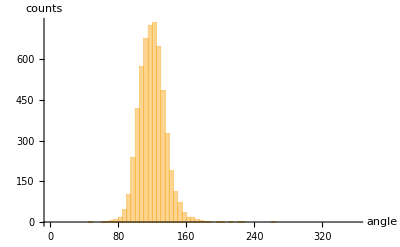

```mathematica
Histogram[{
Flatten[anglesComb,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[anglesComb,1]]
StandardDeviation[Flatten[anglesComb,1]]
```

120.

15.4072

## Domain statistics

## Image 1

Determine the domains alone:

```mathematica
domainIm=Pruning[Pruning@branchImPrun,Infinity]
```

-Graphics-

```mathematica
domains=MorphologicalComponents[ColorNegate@domainIm,"CornerNeighbors"->False];
```

```mathematica
domains//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas=SortBy[ComponentMeasurements[domains,{"Area","Holes"}],Values[#][[1]]&][[;;-3]];
```

```mathematica
domainInds=Keys@domainMeas;
```

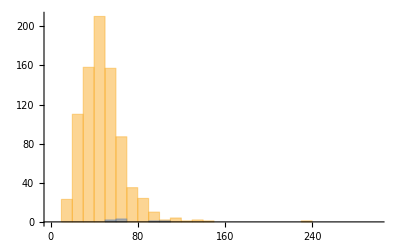

```mathematica
Histogram[{dx^2Select[Values@domainMeas,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas,#[[2]]>=1&][[All,1]]},{0,300,10}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds}],#>0&];,b]
```

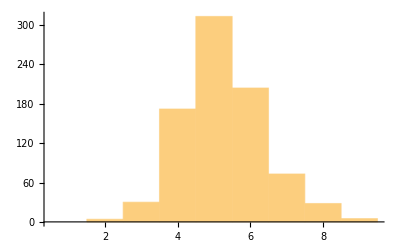

```mathematica
Histogram[cornerNumber,{0.5,10,1}]
```

```mathematica
N@Mean[cornerNumber]
```

5.27404

```mathematica
N@StandardDeviation[cornerNumber]
```

1.20344

## Image 2

Determine the domains alone:

```mathematica
domainIm2=Pruning[Pruning@branchImPrun2,Infinity];
```

```mathematica
domains2=MorphologicalComponents[ColorNegate@domainIm2,"CornerNeighbors"->False];
```

```mathematica
domains2//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas2=SortBy[ComponentMeasurements[domains2,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds2=Keys@domainMeas2;
```

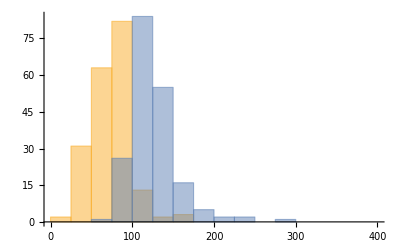

```mathematica
Histogram[{dx^2Select[Values@domainMeas2,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas2,#[[2]]>=1&][[All,1]]},{0,400,25}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber2=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains2,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints2,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds2}],#>0&];,b]
```

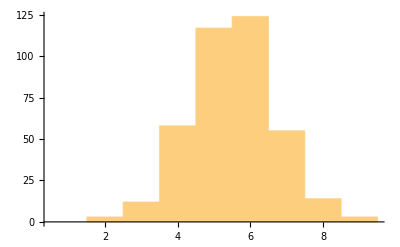

```mathematica
Histogram[cornerNumber2,{0.5,10,1}]
```

```mathematica
N@Mean[cornerNumber2]
```

5.53351

```mathematica
N@StandardDeviation[cornerNumber2]
```

1.23532

## Combined

```mathematica
domainMeasComb=Join[domainMeas,domainMeas2];
cornerNumberComb=Join[cornerNumber,cornerNumber2];
```

```mathematica
Max[dx^2Values[domainMeasComb][[All,1]]]
```

277.244

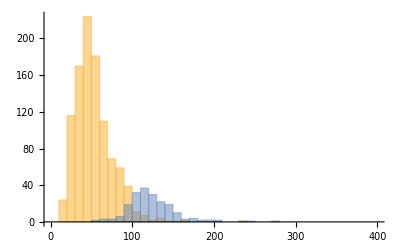

```mathematica
Histogram[{dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]},{0,400,10}]
```

```mathematica
Mean/@{dx^2Values[domainMeasComb][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]}
```

{64.3854,52.8108,123.771}

```mathematica
Max[cornerNumberComb]
```

12

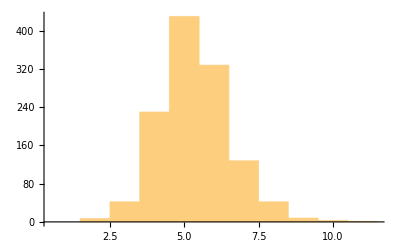

```mathematica
Histogram[cornerNumberComb,{0.5,12,1}]
```

```mathematica
Length@Select[cornerNumberComb,#>10&]
```

2

```mathematica
N@Mean[cornerNumberComb]
N@StandardDeviation[cornerNumberComb]
```

5.35656

1.21917